```mathematica
hedge=Flatten[Import["c:\\book1.txt","Table"],1];
```

```mathematica
Length[hedge]
```

892

```mathematica
g=FinancialData["DAX","1.1.2000"];
```

```mathematica
dax=Transpose[g][[2]][[1;;Length[hedge]]];
```

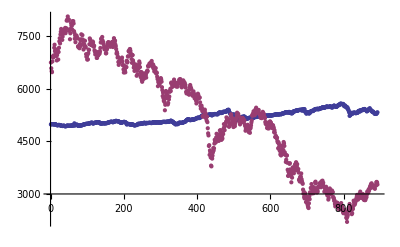

```mathematica
ListPlot[{hedge,dax}]
```

```mathematica
hedge=Log[hedge];dax=Log[dax];
```

```mathematica
hedge=Differences[hedge];
```

```mathematica
dax=Differences[dax];
```

```mathematica
w=Transpose[{hedge,dax}];
```

```mathematica
w=Sort[w,#1[[1]]<#2[[1]]&];
```

```mathematica
hedge=Transpose[w][[1]];
dax=Transpose[w][[2]];
```

```mathematica
w[[2]]
```

{-0.0117745,0.0306036}

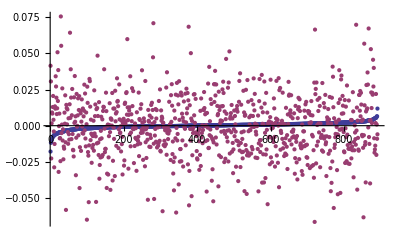

```mathematica
ListPlot[Transpose[w],PlotRange->All]
```

```mathematica
nN=20;wN=Length[hedge];
m0=Min[Transpose[w][[1]]]
Max[Transpose[w][[1]]]
m1=Min[Transpose[w][[2]]]
Max[Transpose[w][[2]]]
f0=(nN-1)/(Max[Transpose[w][[1]]]-m0)
f1=(nN-1)/(Max[Transpose[w][[2]]]-m1)
d=1/wN//N
```

-0.0178719

0.0118256

-0.0665223

0.0755268

639.785

133.757

0.00112233

```mathematica
F={};For[i=1,i≤wN,i++,
For[j=1,j≤wN,j++,
m=0;
If[w[[j,1]]<=w[[i,1]]  && w[[j,2]]≤w[[i,2]],m++;];
];
AppendTo[F,{w[[i,1]],w[[i,2]],m/wN}];
]
```

$Aborted

```mathematica
U={};nN=20;For[i=0,i≤nN,i++,
AppendTo[U,{min0,i/nN*(max1-min1)+min1,0}];
]
For[i=0,i≤nN,i++,
AppendTo[U,{i/nN*(max0-min0)+min0,min1,0}];
]
For[i=0,i≤nN,i++,
AppendTo[U,{max0,i/nN*(max1-min1)+min1,Length[Select[w,#[[1]]<=max0  && #[[2]]<=i/nN*(max1-min1)+min1&]]/wN}];
]
For[i=0,i≤nN,i++,
AppendTo[U,{i/nN*(max0-min0)+min0,max1,Length[Select[w,#[[2]]<=max1  && #[[1]]<=i/nN*(max0-min0)+min0&]]/wN}];
]
```

```mathematica
wN=Length[hedge];
min0=Min[Transpose[w][[1]]];
max0=Max[Transpose[w][[1]]];
min1=Min[Transpose[w][[2]]];
max1=Max[Transpose[w][[2]]];
```

```mathematica
U={};sdax=Sort[dax];AppendTo[U,{max0,max1,1}];

For[i=1,i≤wN,i++,
(*AppendTo[U,{hedge[[i]],max1,(i-1)/wN}];*)
AppendTo[U,{max0,sdax[[i]],(i-1)/wN}];
AppendTo[U,{min0,sdax[[i]],0}];
]
```

```mathematica
F={};For[i=1,i≤wN,i++,
AppendTo[F,{w[[i,1]],w[[i,2]],Length[Select[w,#[[1]]<w[[i,1]]  && #[[2]]<w[[i,2]]&]]/wN}];
]
```

```mathematica
W=Join[F,U];
```

```mathematica
ListPointPlot3D[W]
```

-Graphics3D-

```mathematica
ww={};
For[i=1,i≤wN,i++,
AppendTo[ww,Select[W,#[[2]]==sdax[[i]]&]];
]
```

```mathematica
Length[W]
Length[Flatten[ww,1]]
```

2674

2674

```mathematica
Sort[fi[[2]],#1[[1]]<#2[[1]]&]//N//MatrixForm
```

(-0.0178719 | -0.0145212 | 0.
-0.000530372 | -0.0145212 | 0.0583614
0.0118256 | -0.0145212 | 0.224467)

```mathematica
fi=ww[[200;;250]];
ListPointPlot3D[fi]
```

```mathematica
Po[a_,b_]:=If[b==0,1,If[b==-1,0,a^b]];
```

```mathematica
B[n_,i_,x_]:=Binomial[n,i] Po[x,i] Po[1-x,n-i];
```

```mathematica
nn=Length[fi]
```

51

```mathematica
t=0.1;
```

```mathematica
c=.
```

```mathematica
c[t0_,fi0_]:=Module[{t=t0,fi=fi0,i,j,k,no,cc={},e},For[i=1,i≤nn,i++,
e=Sort[fi[[i]],#1[[1]]<#2[[1]]&];no=Length[fi[[i]]];

For[j=1,j≤ no,j++,
For[k=1,k≤ no-j,k++,
e[[k]]=e[[k]](1-t)+e[[k+1]]t;
];
];
AppendTo[cc,e[[1]]];
];

cc
]
```

```mathematica
erg[a0_,b0_,fi0_]:=Module[{e=c[a0,fi0],t=b0,i,j,k,no},

no=Length[e];

For[j=1,j≤ no,j++,
For[k=1,k≤ no-j,k++,
e[[k]]=e[[k]](1-t)+e[[k+1]]t;
];
];
e[[1]]
]
```

```mathematica
erg[0.1,0.1,fi]
```

{-0.0143759,-0.0142983,0.0207922}

```mathematica
Erg=Flatten[Table[erg[x,y,fi],{x,0,1,0.1},{y,0,1,0.1}],1];
```

```mathematica
ListPointPlot3D[Erg]
```

-Graphics3D-